# Angular distribution of neutron from photon - disintergating Deuteron

```mathematica
(* at CM frame *)
(* the Deuteron is moving back with momentum pD = p light *)
```

```mathematica
(* before collision *)
(* gamma ray *)
{Eγ, p}
Eγ==p
(* Deuteron *)
{ED,pD}
ED==√(pD^2+mD^2)
EB =mD - mp-mn(* Blinding energy *)
```

```mathematica
(* after collision, the Deuteron dis-intergrate into proton and neutron *)
(* proton *)
{Epc,ppc Cos[θpc],ppc Sin[θpc],0}
Epc ==√(ppc^2+mp^2)
(* neutron *)
{Enc, pnc Cos[-θnc],pnc Sin[-θnc],0}
Enc ==√(pnc^2+mn^2)
```

```mathematica
(* conservation of energy *)
Eγ+ED = Epc+Enc
(* conservation of momentum *)
ppc =pnc
```

```mathematica
Solve[p+√(p^2+(mD)^2)==√(pnc^2+mp^2)+√(pnc^2+mn^2),pnc]//Simplify
```

```mathematica
{{pnc->-1/(2 mD^2)(√(mD^6+mD^2 (mn^2-mp^2)^2-2 (mn^2-mp^2)^2 p (-p+√(mD^2+p^2))-2 mD^4 (mn^2+mp^2-p (p+√(mD^2+p^2)))))},{pnc->1/(2 mD^2)(√(mD^6+mD^2 (mn^2-mp^2)^2-2 (mn^2-mp^2)^2 p (-p+√(mD^2+p^2))-2 mD^4 (mn^2+mp^2-p (p+√(mD^2+p^2)))))}}
```

```mathematica
(* take the positive value *)pnc =1/(2 mD^2)(√(mD^6+mD^2 (mn^2-mp^2)^2-2 (mn^2-mp^2)^2 p (-p+√(mD^2+p^2))-2 mD^4 (mn^2+mp^2-p (p+√(mD^2+p^2)))))
```

```mathematica
(* change to Lab frame that the Deuteron is stable *)
(* the lorentz transform is *)
L[β_]:= 1/(√(1-β^2)){{1,β,0,0},{β,1,0,0},{0,0,1,0},{0,0,0,1}}
```

```mathematica
L[β].{√(p^2+mD^2),p,0,0}
```

{(√(mD^2+p^2))/(√(1-β^2))+(p β)/(√(1-β^2)),p/(√(1-β^2))+(√(mD^2+p^2) β)/(√(1-β^2)),0,0}

```mathematica
Solve[p/(√(1-β^2))+(√(mD^2+p^2) β)/(√(1-β^2))==0,β]
```

{{β→-p/(√(mD^2+p^2))}}

```mathematica
L[-p/(√(mD^2+p^2))].{√(pnc^2+mn^2), pnc Cos[-θnc],pnc Sin[-θnc],0}//Simplify
```

{(√(mD^2+p^2) √(mn^2+pnc^2)-p pnc Cos[θnc])/(√(mD^2/(mD^2+p^2)) √(mD^2+p^2)),(-p √(mn^2+pnc^2)+√(mD^2+p^2) pnc Cos[θnc])/(√(mD^2/(mD^2+p^2)) √(mD^2+p^2)),-(pnc Sin[θnc])/(√(mD^2/(mD^2+p^2))),0}

```mathematica
(* put in physical number *)
mD=1876.1244;
p=2.76;
mp=938.272013;
mn=939.565346;
```

```mathematica
(* the energy distribution is *)
En=(√(mD^2+p^2) √(mn^2+pnc^2)-p pnc Cos[θnc])/(√(mD^2/(mD^2+p^2)) √(mD^2+p^2))/.{pnc->1/(2 mD^2)(√(mD^6+mD^2 (mn^2-mp^2)^2-2 (mn^2-mp^2)^2 p (-p+√(mD^2+p^2))-2 mD^4 (mn^2+mp^2-p (p+√(mD^2+p^2)))))}//Simplify
```

```mathematica
En//Simplify
```

940.091-0.0461769 Cos[θnc]

```mathematica
(* momentum *)
pn=√(((-p √(mn^2+pnc^2)+√(mD^2+p^2) pnc Cos[θnc])/(√(mD^2/(mD^2+p^2)) √(mD^2+p^2)))^2+((pnc Sin[θnc])/(√(mD^2/(mD^2+p^2))))^2)/.{pnc->1/(2 mD^2)(√(mD^6+mD^2 (mn^2-mp^2)^2-2 (mn^2-mp^2)^2 p (-p+√(mD^2+p^2))-2 mD^4 (mn^2+mp^2-p (p+√(mD^2+p^2)))))}//FullSimplify
```

√(987.182-86.8209 Cos[θnc]+5.68434×10^-14 Cos[2 θnc])

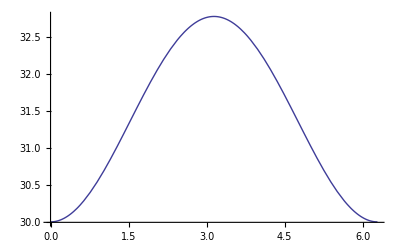

```mathematica
Plot[pn,{θnc,0,2π}]
```

```mathematica
(* angle at lab *)
θn=ArcTan[((pnc Sin[θnc])/(√(mD^2/(mD^2+p^2))))/((-p √(mn^2+pnc^2)+√(mD^2+p^2) pnc Cos[θnc])/(√(mD^2/(mD^2+p^2)) √(mD^2+p^2)))]/.{pnc->1/(2 mD^2)(√(mD^6+mD^2 (mn^2-mp^2)^2-2 (mn^2-mp^2)^2 p (-p+√(mD^2+p^2))-2 mD^4 (mn^2+mp^2-p (p+√(mD^2+p^2)))))}//FullSimplify
```

ArcTan[(58889.7 Sin[θnc])/(-2594.65+58889.7 Cos[θnc])]

```mathematica
Solve[Tan[x]==(58889.667980759295 Sin[θnc])/(-2594.647076597241+58889.667980759295 Cos[θnc]),θnc]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θnc→-1. ArcCos[(0.5 (8.05305×10^31 Tan[x]^2-1.82599×10^33 √(1.00195+1. Tan[x]^2)))/(9.13885×10^32+9.13885×10^32 Tan[x]^2)]},{θnc→ArcCos[(0.5 (8.05305×10^31 Tan[x]^2-1.82599×10^33 √(1.00195+1. Tan[x]^2)))/(9.13885×10^32+9.13885×10^32 Tan[x]^2)]},{θnc→-1. ArcCos[(0.5 (8.05305×10^31 Tan[x]^2+1.82599×10^33 √(1.00195+1. Tan[x]^2)))/(9.13885×10^32+9.13885×10^32 Tan[x]^2)]},{θnc→ArcCos[(0.5 (8.05305×10^31 Tan[x]^2+1.82599×10^33 √(1.00195+1. Tan[x]^2)))/(9.13885×10^32+9.13885×10^32 Tan[x]^2)]}}

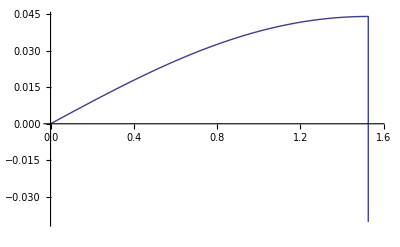

```mathematica
Plot[θn-θnc,{θnc,0,π/2}]
```

```mathematica
(*momentum in lab frame *)
ArcCos[(0.5 (8.053052305435749*^31 Tan[x]^2+1.825994177443105*^33 √(1.001945011901244+1. Tan[x]^2)))/(9.138845525009615*^32+9.138845525009615*^32 Tan[x]^2)]
```

```mathematica
pn=√(((-p √(mn^2+pnc^2)+√(mD^2+p^2) pnc Cos[θnc])/(√(mD^2/(mD^2+p^2)) √(mD^2+p^2)))^2+((pnc Sin[θnc])/(√(mD^2/(mD^2+p^2))))^2)/.{pnc->1/(2 mD^2)(√(mD^6+mD^2 (mn^2-mp^2)^2-2 (mn^2-mp^2)^2 p (-p+√(mD^2+p^2))-2 mD^4 (mn^2+mp^2-p (p+√(mD^2+p^2))))),θnc->ArcCos[(0.5 (8.053052305435749*^31 Tan[x]^2+1.825994177443105*^33 √(1.001945011901244+1. Tan[x]^2)))/(9.138845525009615*^32+9.138845525009615*^32 Tan[x]^2)]}//FullSimplify
```

1.09423×10^-33 √(Cos[x]^4 (8.2448×10^68+8.21285×10^68 Tan[x]^4-7.24411×10^67 √(1.00195+1. Tan[x]^2)+Tan[x]^2 (1.64576×10^69-7.24411×10^67 √(1.00195+1. Tan[x]^2))))

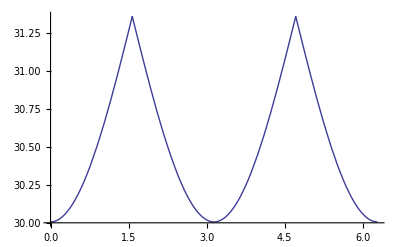

```mathematica
Plot[pn,{x,0,2π}]
```